```mathematica
X[{θ_,ϕ_}]:={Cos[π/180 θ]Cos[π/180 ϕ],Sin[π/180 θ]Cos[π/180 ϕ],Sin[π/180 ϕ]};

Ortho[{x1_,y1_},{x2_,y2_}]:=Module[{θ1,ϕ1,θ2,ϕ2},
{θ1,ϕ1,θ2,ϕ2}=π/180{x1,y1,x2,y2};
N[(360  60)/(2π) ArcCos[Cos[θ1-θ2] Cos[ϕ1] Cos[ϕ2]+Sin[ϕ1] Sin[ϕ2]]]
];
```

```mathematica
Graphe[{θ1_,ϕ1_},{θ2_,ϕ2_}]:=Module [{ρ,e,c,s,M,m,n},
ρ=0.3;
{m,n}={20,10};
e=((θ2-θ1)^2+(ϕ2-ϕ1)^2)^(1/2);
{c,s}={(θ2-θ1)/e,(ϕ2-ϕ1)/e};
M:=({{c, -s}, {+s, c}});
Table[N[M.{e/m i,ρ e/m j}+{θ1,ϕ1}],{i,0,m},{j,-n,n}]]
```

```mathematica
AncreDep={8.05,47.3};
AncreArr= {226.88,-47.22};
Loc = Graphe[AncreDep,AncreArr];
{Maxi,Maxj,Coord}=Dimensions[Loc]
```

{21,21,2}

```mathematica
ProgrammationDynamique[Start_]:=Module[{ Spread,Graphe,ProgrDyn},
Spread=4;

ProgrDyn[r_]:=Module[{Etabli,Posi},
Do[Etabli=Table[Graphe[[r-1,j,2]]+Ortho[Loc[[r-1,j]],Loc[[r,k]]],{j,1,Maxj}];{{Posi}}=Position[Etabli,Min[Etabli]];
If[Abs[k-Posi]≤Spread,Graphe[[r,k]]={{{r-1,Posi},{r,k}},Min[Etabli]}],{k,1,Maxj}]
];

Graphe=Table[{0,10^6},{i,1,Maxi},{j,1,Maxj}];
Graphe[[1,Start]]={1,0};
Do[ProgrDyn[r],{r,2,Maxi}];

Transpose[Graphe]
]; (* Programmation Dynamique *)
```

```mathematica
Decision=ProgrammationDynamique[15];
(*OutputForm[Decision]*)
```

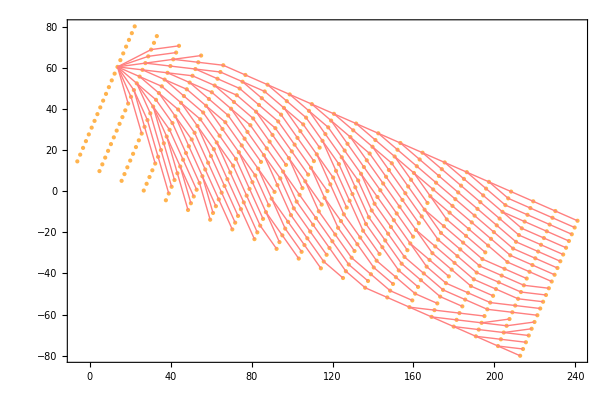

```mathematica
G1=Table[Graphics[{RGBColor[1,0.7,0.3], Point[Loc[[i,j]]]}],{i,1,Maxi},{j,1,Maxj}];
G2=Select[Flatten[Decision,1],(Last[#]<1000000)&&(Last[#]>0.1)&];
DimG2=First[Dimensions[G2]];
G3=Table[First[G2[[i]]],{i,1,DimG2}];
G4=Table[{Loc[[First[G3[[i]]][[1]],First[G3[[i]]][[2]]]],Loc[[Last[G3[[i]]][[1]],Last[G3[[i]]][[2]]]]},{i,1,DimG2}];
G5=Table[Graphics[{RGBColor[1,0.5,0.5],Line[{G4[[i,1]],G4[[i,2]]}]}],{i,1,DimG2}];
Show[G1,G5,Frame-> True]
```

```mathematica
G6=Table[{N[X[G4[[i,1]]]],N[X[G4[[i,2]]]]},{i,1,DimG2}];
G7=Table[Graphics3D[{RGBColor[1,0.5,1],Line[{G6[[i,1]],G6[[i,2]]}]}],{i,1,DimG2}];
Earth=Graphics3D[Sphere[{0,0,0}]];
Show[Earth,G7]
```

-Graphics3D-